## 133La

```mathematica
ClearAll["Global`*"]
```

```mathematica
yrastEn=Sort[{8760,7803,6880.5,5998.8,5164.9,4320.9,3245.4,2245.3,1391.1,730.9,358.08}];
wob1En=Sort[{5067.5,3955.5,2999.9,2203.9,1477.9}];
yrastSpin=Table[i/2,{i,11,55,4}];
wob1Spin=Table[i/2,{i,17,33,4}];
```

```mathematica
omega[data_]:=Table[1/2(data[[i]]-data[[i-1]])/1000,{i,2,Length[data]}];
```

```mathematica
omegaYrast=omega[yrastEn];
omegawob1=omega[wob1En];
```

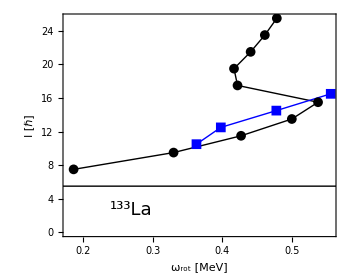

```mathematica
ListPlot[{Table[{omegaYrast[[i]],yrastSpin[[i+1]]},{i,1,Length[omegaYrast]}],Table[{omegawob1[[i]],wob1Spin[[i+1]]},{i,1,Length[omegawob1]}]},Joined->True,PlotMarkers->{Automatic, Medium},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"ω_rot [MeV]","I [ℏ]"},LabelStyle->{18,Bold,Black,FontFamily->"Times"},PlotRange->Full,ImageSize->350,FrameTicks->{{Automatic,None},{{0.2,0.3,0.4,0.5},None}},Epilog->{Style[Line[{{-100,5.5},{100,5.5}}],Thick,Magenta,DotDashed,Opacity[1]],Inset[Style[Framed[Row[{Superscript["","133"],"La"}]],FontFamily->"Times",Black,18],Scaled[{0.25,0.12}]]},PlotStyle->{{Black,Thick},{Blue,Thick},{Red,Thick}}]
```